Jalil Villalobos Alva

Beginning Mathematica and Wolfram for Data Science: ML & DL              <     Ξ

Edited by Hao Feng

## Neural Networks Framework

This chapter explores training a neural network model in the Wolfram Language, how to access the results and the trained network. You review the basic commands to export and import a net model. You end the chapter by exploring the Wolfram Neural Net Repository and reviewing the LeNet network model.

### Training a Neural Network

The Wolfram Language contains a very useful command that automates neural
network model training. This command is NetTrain. Training a neural network
consists of fine-tuning the internal parameters of the neural network. The whole point
is that the parameters can be learned during training. This general process is done
by an optimization algorithm called gradient descent, which is computed with the
backpropagation algorithm.

#### Data Input

With NetTrain, data can be entered in different forms. First, the net model goes as the first argument, followed by the input → target, {inputs, ...} → {target, ...} or the name of the data or dataset. Once the net model is defined, the next argument is the data, followed by an optional argument of All. The All option creates a NetTrainResultsObject, which shows the NetTrain results panel after the computation and stores all relevant information about the trained model. The options for training the model are entered as the last arguments. Standard options used in layers and containers are available in NetTrain.

The next example uses the perceptron model to build a linear classifier. The data to
be classified is shown in the following plot.

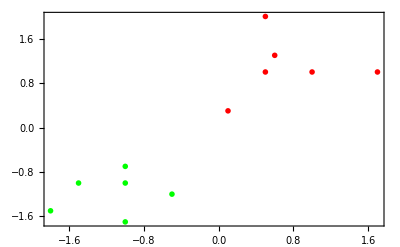

```mathematica
plt=ListPlot[{{{-1.8,-1.5},{-1,-1.7},{-1.5,-1},{-1,-1},{-0.5,-1.2},{-1,-0.7}},{{1,1},{1.7,1},{0.5,2},{0.1,0.3},{0.5,1},{0.6,1.3}}},PlotMarkers->"OpenMarkers",Frame->True,PlotStyle->{Green,Red}]
```

Let’s define the data, target values, and the training data.

```mathematica
data={{-1.8,-1.5},{-1,-1.7},{-1.5,-1},{-1,-1},{-0.5,-1.2},{-1,-0.7},{1,1},{1.7,1},{0.5,2},{0.1,0.3},{0.5,1},{0.6,1.3}};
```

```mathematica
target={-1,-1,-1,-1,-1,-1,1,1,1,1,1,1};
```

```mathematica
trainData=MapThread[#1->{#2}&,{Standardize[data],target},1];
```

The Standardize function is crucial in the latter code because it normalizes the input
data before training the neural network. This step ensures that each feature contributes equally to the learning process during the training phase, preventing any single feature from dominating the others. This process can lead to faster convergence during training and improves the overall performance of the net model. Next, let’s define the net model.

```mathematica
model=NetChain[{LinearLayer[1,"Input"->2],ElementwiseLayer[Ramp[#]&]}];
```

#### Training Phase

Having prepared the data and the model, you proceeded to train the model. Once the training begins, a progress information panel appears with four main results.
• Summary: contains relevant information about the batches, rounds, and time rates
• Data: involves processed data information
• Method: shows the method used, batch size, and device used for training
• Round: the current state of loss value

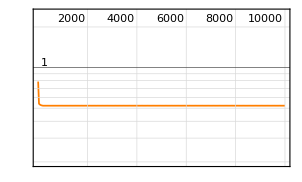
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:10000  rounds:10000  time:21s  examples/s:5855
data | ,,  training examples:12  processed examples:120000  skipped examples:0
method | ,,  ADAMoptimizer  batch size12CPU
round | ,,  loss:5.22×10^-1
 | rounds
loss | -Graphics- | 
 | ]

```mathematica
net=NetTrain[model,trainData,All,LearningRate->0.01,PerformanceGoal->"TrainingSpeed",TrainingProgressReporting->"Panel",TargetDevice->"CPU",RandomSeeding->88888,WorkingPrecision->"Real64"]
```

The Adam optimizer is a variant of the Stochastic gradient descent, which you see
later. The object generated is called NetTrainResultsObject.

#### Model Implementation

Once the training is done, getting the trained net and model implementation is as
follows.

```mathematica
trainedNet1=net["TrainedNet"]
```

NetChain[…]

Let’s look at how the trained net identifies each point by plotting the boundaries with
a density plot.

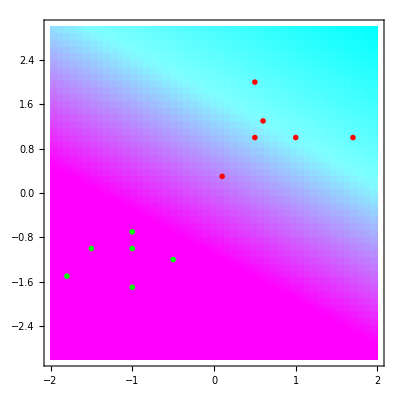

```mathematica
Show[DensityPlot[trainedNet1[{x,y}],{x,-2,2},{y,-3,3},PlotPoints->50,ColorFunction->(RGBColor[1-#,2*#,1]&)],plt]
```

The graphic shows that the boundaries are not well defined and that points near zero might be misclassified. This result can be attributed to the ramp function, which gives
0 if it receives any negative number, but for any positive value, it returns that value. This model can still be improved, perhaps by changing the activation function to a hyperbolic tangent to have robust boundaries.

#### Batch Size and Rounds

If the batch size is not indicated, it has an automatic value, almost always a value of
64 or powers of two. Remember that the batch size indicates the number of examples
the model uses in training before updating the internal parameters of the model. The
number of batches is the division of the examples within the training dataset by the
batch size. The processed examples are the number of rounds (epochs) multiplied by the number of training examples. The batch size is generally chosen to divide the training set’s size evenly. The MaxTrainingRounds option determines the number of times the training dataset is passed through during the training phase. When you go through the entire training set just once, it’s called an epoch. To better understand this, a batch size of 12 was automatically chosen in the earlier example, which is equal to the number of examples in the training set. This means that it enters a batch of 12/12 -> 1 for epoch or round. Now, the number of epochs was automatically chosen to 10000; this tells you that there are 1 * 10000 batches. Also, the number of processed examples is 12 * (10000), which is equal to 120000. If the batch size does not evenly divide the training set, the final batch has fewer examples than the other batches.

Furthermore, adding a loss function layer to the container or the loss with the
LossFunction -> Loss Layer option has the same effect. In this case, you use the
MeanSquaredLossLayer as the loss function option, change the activation function to
Tanh[x], set the Batchsize to 5, and adjust MaxTrainingRounds to 1000.

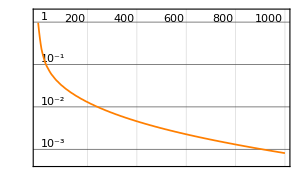
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:3000  rounds:1000  time:3.5s  examples/s:4282
data | ,,  training examples:12  processed examples:15000  skipped examples:0
method | ,,  ADAMoptimizer  batch size5CPU
round | ,,  loss:8.12×10^-4
 | rounds
loss | -Graphics- | 
 | ]

```mathematica
net2=NetTrain[NetChain[{LinearLayer[1,"Input"->2],ElementwiseLayer[Tanh[#]&]}],trainData,All,LearningRate->0.01,PerformanceGoal->"TrainingSpeed",TrainingProgressReporting->"Panel",TargetDevice->"CPU",RandomSeeding->88888,WorkingPrecision->"Real64",LossFunction->MeanSquaredLossLayer[],BatchSize->5,MaxTrainingRounds->1000]
```

Let’s determine the classification.

```mathematica
trainedNet2=net2["TrainedNet"];
```

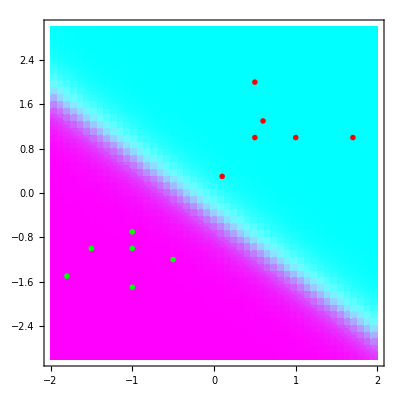

```mathematica
Show[DensityPlot[trainedNet2[{x,y}],{x,-2,2},{y,-3,3},PlotPoints->50,ColorFunction->(RGBColor[1-#,2*#,1]&)],plt]
```

The previous models represent a prediction of a linear layer, in which this
classification is compared with the targets so that the error is less and less.

To obtain the graph that shows the value of the error according to the number
of rounds carried out in the training, you do it through the properties of the trained
network. You can also see the network model’s appearance once the loss function
is added.

```mathematica
Dataset[{Association["LossPlot"->net2["LossPlot"]],Association["NetGraph"->net2["TrainedNet"]]}]
```

To see the network used for training, execute the next code. Mathematica
automatically adds a loss function to the neural network based on the model’s layers.

```mathematica
net2["TrainingNet"]
```

NetGraph[…]

To see the model’s properties, you add the string Properties as an argument.

```mathematica
net2["Properties"]
```

{ArraysLearningRateMultipliers,BatchesPerRound,BatchesPerSecond,BatchLossList,BatchMeasurements,BatchMeasurementsLists,BatchSize,BestValidationRound,CheckpointingFiles,ExamplesProcessed,FinalLearningRate,FinalPlots,InitialLearningRate,InternalVersionNumber,LossPlot,MeanBatchesPerSecond,MeanExamplesPerSecond,NetTrainInputForm,OptimizationMethod,ReasonTrainingStopped,RoundLoss,RoundLossList,RoundMeasurements,RoundMeasurementsLists,RoundPositions,SkippedTrainingData,TargetDevice,TotalBatches,TotalRounds,TotalTrainingTime,TrainedNet,TrainingExamples,TrainingNet,TrainingUpdateSchedule,ValidationExamples,ValidationLoss,ValidationLossList,ValidationMeasurements,ValidationMeasurementsLists,ValidationPositions}

#### Training Method (NetTrain)

Let’s look at the training method for the previous network with OptimizationMethod. Some variants of the gradient descent algorithm are related to batch size. The first one
is the stochastic gradient descent (SGD). The SGD takes a single training batch at a
time before taking another step. This algorithm goes through the training examples in
a stochastic form—without a sequential pattern and only one instance at a time. The second variant is the batch gradient descent, meaning that the batch size is set to the
size of the training set. This method utilizes all training examples and makes only one
update of the internal parameters. The third variant is the mini-batch gradient descent, which consists of dividing the training set into partitions smaller than the whole dataset to update the model’s internal parameters to achieve convergence frequently. To see a mathematical of the SGD and mini-batch SGD, visit the article “Efficient Mini-Batch Training for Stochastic Optimization,” by Mu Li, Tong Zhang, Yuqiang Chen, and Alexander J. Smola (2014, August: pp. 661-670; In Proceedings of the 20th ACM SIGKDD international conference on Knowledge discovery and data mining).

```mathematica
net2["OptimizationMethod"]
```

{ADAM,Beta1→0.9,Beta2→0.999,Epsilon→1/100000,GradientClipping→None,L2Regularization→None,LearningRate→0.01,LearningRateSchedule→None,WeightClipping→None}

The method automatically chosen is the Adam optimizer, which uses the SGD method with an adapted learning rate. The other available methods are the RMSProp, SGD, and the SignSGD. Within the available methods, there are also options to indicate the learning rate, when to scale, when to use the L^2 regularization, the gradient, and weight clipping.

#### Measuring Performance

In addition to the methods, you can establish what measures to consider during the
training phase. These options depend on the type of loss function used and which is
intrinsically related to the task, like classification, regression, and clustering. In the
case of MeanSquaredLossLayer or MeanAbsoluteLossLayer, the common option is
MeanDeviation, which is the absolute value of the average of the residuals. MeanSquare is the mean square of the residuals, RSquared is the coefficient of determination, and standard deviation is the root mean square of the residuals. After completing the training, the measure appears in the net results. The soft sign activation function is used in this example to try out a different activation function and observe its use.

```mathematica
net3=NetTrain[NetChain[{LinearLayer[1,"Input"->2],ElementwiseLayer["SoftSign"]}],trainData,All,LearningRate->0.01,PerformanceGoal->"TrainingSpeed",TrainingProgressReporting->"Panel",TargetDevice->"CPU",RandomSeeding->88888,WorkingPrecision->"Real64",Method->"ADAM",LossFunction->MeanSquaredLossLayer[],BatchSize->5,MaxTrainingRounds->1000,TrainingProgressMeasurements->{"MeanDeviation","MeanSquare","RSquared","StandardDeviation"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:3000  rounds:1000  time:6.1s  examples/s:2477
data | ,,  training examples:12  processed examples:15000  skipped examples:0
method | ,,  ADAMoptimizer  batch size5CPU
round | ,,  loss:2.25×10^-2  res. mean dev.:1.42×10^-1  res. mean sqr.:2.25×10^-2  res. r.b2:9.77×10^-1  res. s.d.:1.5×10^-1
 | 
 | ]

#### Model Assessment

To access the values of the measures chosen, use the NetResultsObject. In the case
of the training set values, these are found in the properties of RoundLoss (gives the
average value of the loss), RoundLossList (returns the average values of the loss during
training), RoundMeasurements (the measurements of the training of the last round),
and RoundMeasurementsLists (the specified measurements for each round).

```mathematica
net3[#]&/@{"RoundMeasurements"}//Dataset[#]&
```

To get all the plots, use the FinalPlots option.

```mathematica
net3["FinalPlots"]//Dataset
```

To replicate the plots of the measurements, extract the values of the measurements
of each round with RoundMeasurementsLists.

```mathematica
measures=net3[#]&/@{"RoundMeasurementsLists"};
Keys[measures]
```

{{Loss,MeanDeviation,MeanSquare,RSquared,StandardDeviation}}

Let’s plot the values for each round, starting with Loss and finishing with
StandardDeviation. You can also see how the network model makes the classification
boundaries.

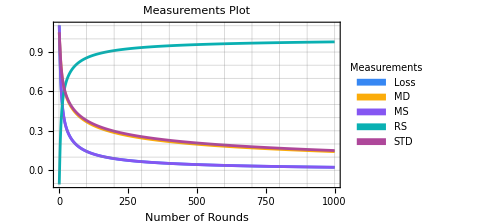
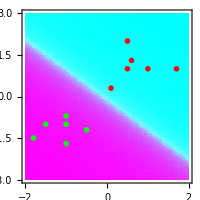
-Graphics- | -Graphics-

```mathematica
trainedNet3=net3["TrainedNet"];
Grid[{{ListLinePlot[{
measures[[1,1]],
measures[[1,2]],
measures[[1,3]],
measures[[1,4]],
measures[[1,5]]},
PlotStyle->Table[ColorData[101,i],{i,1,5}],Frame->True,FrameLabel->{"Number of Rounds",None},PlotLabel->"Measurements Plot",GridLines->All,PlotLegends->SwatchLegend[{
Style["Loss",#],Style["MD",#],Style["MS",#],Style["RS",#],Style["STD",#]},
LegendLabel->Style["Measurements",#],LegendFunction->(Framed[#,RoundingRadius->5,Background->LightGray]&)],ImageSize->Medium]&[Black],Show[DensityPlot[trainedNet3[{x,y}],{x,-2,2},{y,-3,3},PlotPoints->50,ColorFunction->(RGBColor[1-#,2*#,1]&)],plt,ImageSize->200]}}]
```

The Loss and MeanSquared have the same values (since the loss is a mean squared
error loss function), which is why the two graphics overlap. The mean deviation and
standard deviation have similar values but not the same. Three models are constructed, and the activation function changes in each process. Looking at the plots, you see how each function changes how the neural network model learns from the training data. In the previous examples, the graphics were the loss plot for the training process and other measurements related to the means squared loss layer. Make sure to consult the documentation to confirm the measurements’ names; remember that not all measurements apply to all loss functions.

In the subsequent section, you see how to generate the loss plot and the validation
plot during the training phase to validate that the LeNet model is learning during
training and how well the model can perform in data never seen before (validation set).

#### Exporting a Neural Network

Once a net model has been trained, you can export this trained net to a WLNet format so that the net can be used without the need for training in the future. The export method also works for uninitialized network architectures.

```mathematica
Export["~/Desktop/TrainedNet3.wlnet",net3["TrainedNet"]]
```

~/Desktop/TrainedNet3.wlnet

Importing them back is done precisely as any other file, but imported elements can
be specified. Net imports the net model and all initialized arrays; UninitializedNet and
ArrayList imports for the numeric array’s objects of the linear layers; ArrayAssociation
imports for the numeric arrays in association form, and WLVersion is used to see the
version of the Wolfram Language used to build the net. The following dataset shows all the options

```mathematica
Dataset@AssociationMap[Import["~/Desktop/TrainedNet3.wlnet",#]&,{"Net","UninitializedNet","ArrayList","ArrayAssociation","WLVersion"}]
```

### Wolfram Neural Net Repository

The Wolfram Neural Net Repository is a free-access website containing a repertoire
of various pre-trained neural network models. The models are categorized by the
input and data types, be it audio, image, numeric array, or text. Furthermore, they are
also categorized by the kind of task they perform, from audio analysis or regression to
classification. The main page of the website is

https://resources.wolframcloud.com/NeuralNetRepository

Enter https://resources.wolframcloud.com/NeuralNetRepository/ in your
favorite browser to access the web page, or run SystemOpen from Mathematica, which opens the web page in the system’s default browser.

Once the site is loaded, net models can be browsed by either input or task. The
models in this repository are built in the Wolfram Language, allowing you to use them
within Mathematica. This leads to the models being found in a form that can be accessed from Mathematica or the Wolfram Cloud for prompt execution. If you scroll down, you see that the models are structured by name and the data used for training, along with a short description. Such is the case, for example, for the Wolfram AudioIdentify V1 network, which is trained with the AudioSet Data and identifies sounds in audio signals. To browse categories, you can choose the category from the menu.

#### Selecting a Neural Net Model

Once a category is chosen, it shows all the net models associated with the selected input category. Like with the Wolfram Data Repository, once the model is selected, it shows relevant information, where the selected net model is the neural network Wolfram ImageIdentify Net V1.

It is possible to navigate from the website and download the notebook containing
the network model, but it is also possible from Mathematica. In other words, search for network models through ResourceSearch. The example shows the search if you were interested in knowing the models of the networks that contain the word image.

```mathematica
ResourceSearch[{"Name"->"Image","ResourceType"->"NeuralNet"}]//Dataset[#,MaxItems->{4,3}]&
```

The dataset shown has only three columns for display purposes, but you can navigate through the entire dataset using the slider. The columns not shown in the image are Description, Location, and DocumentationLink. The last column provides the link that leads to the web model page.

#### Accessing Inside Mathematica

To access the model architecture, add the object argument; for example, do the following for the Wolfram ImageIdentify Net V1 Network.

```mathematica
ResourceSearch[{"Name"->"Wolfram ImageIdentify","ResourceType"->"NeuralNet"},"Object"]
```

{ResourceObject[…]}

Note: to avoid problems accessing the Wolfram Net Repository from Mathematica, ensure you are logged in to the Wolfram Cloud or your Wolfram account.

The following code is suppressed here to access the pre-trained model, but removing
the semicolon returns the NetChain object of the pre-trained neural network.

```mathematica
ResourceSearch[{"Name"->"Wolfram ImageIdentify","ResourceType"->"NeuralNet"},"Object"][[1]]//ResourceData
```

NetChain[<24>]

#### Retrieving Relevant Information

Information about the model is accessed from ResourceObject. The following is the
relevant information from the ImageIdentify model in a dataset. To see all information in the dataset format, type ResourceObject [“Wolfram ImageIdentify
Net V1”][All]//Dataset [#] &.

```mathematica
Dataset[AssociationMap[ResourceObject["Wolfram ImageIdentify Net V1"],{"Name","RepositoryLocation","ResourceType","ContentElements","Version","Description","TrainingSetInformation","InputDomains","TaskType","Keywords","Attributes","LatestUpdate","DownloadedVersion","Format","ContributorInformation","DOI","Originator","ReleaseDate","ShortName","WolframLanguageVersionRequired"}]]
```

Here, in a few steps, is the way to access the trained neural network and much
relevant information associated with the neural network. It should be noted that the
process is also used to find other resources in the Wolfram Cloud or local resources, not only neural networks, since, in general, ResourceSearch looks for an object within the Wolfram Resource System. Such is the case of the neural network models in the Wolfram Neural Net Repository.

### LeNet Neural Network

The following example examines a neural network model named LeNet. Despite being able to access the model from a Wolfram resource, as you saw previously, performing operations with networks found in the Wolfram Neural Net Repository with the NetModel command is possible. To get a better idea of how this network is used, let’s first look at the description of the network, its name, how it is used, and where it was proposed for the first time.

#### LeNet Model

The neural network LeNet is a convolutional neuronal network within the deep learning field. The neural network LeNet is recognized as one of the first convolutional networks that promoted deep learning. This network was used for character recognition to identify handwritten digits. Today, architectures are based on LeNet neural network architecture, but you focus on the Wolfram Neural Net Repository version. This architecture consists of four key operations: convolution, non-linearity, subsampling, or pooling and classification. To learn more about the LeNet convolutional neural network, see Neural Networks and Deep Learning: A Textbook by Charu C. Aggarwal (Springer, 2018). With NetModel, you can obtain information about the LeNet network that has been previously trained.

```mathematica
NetModel["LeNet Trained on MNIST Data",#]&/@{"Details","ShortName","TaskType","SourceMetadata"}//Column
```

This pioneer work for image classification with convolutional neural nets was released in 1998. It was developed by Yann LeCun and his collaborators at AT&T Labs while they experimented with a large range of machine learning solutions for classification on the MNIST dataset.
LeNet-Trained-on-MNIST-Data
{Classification}
<|Citation→Y. LeCun, L. Bottou, Y. Bengio, P. Haffner, "Gradient-Based Learning Applied to Document Recognition," Proceedings of the IEEE, 86(11), 2278-2324 (1998),Source→http://yann.lecun.com/exdb/lenet,Date→DateObject[{1998},Year,Gregorian,-5.]|>

Note: to access all the properties of a model with NetModel, add properties as the second argument—NetModel[“LeNet Trained on MNISt Data,” “Properties”].

The input this model receives consists of images in grayscale with a size of 28 x 28,
and the model’s performance is 98.5% on the MNIST dataset.

```mathematica
NetModel["LeNet Trained on MNIST Data",#]&/@{"TrainingSetInformation","InputDomains","Performance"}//Column
```

MNIST Database of Handwritten Digits, consisting of 60,000 training and 10,000 test grayscale images of size 28x28.
{Image}
This model achieves 98.5% accuracy on the MNIST dataset.

#### MINST Dataset

This network is used for rating, just as it appears in TaskType. The digits are in a database known as the MNIST database. The MNIST database is an extensive database of handwritten digits that contains 60,000 images for training and 10,000 for testing, the latter being used to get a final estimate of how well the neural net model works. To observe the complete dataset, you load it from the Wolfram Data Repository with ResourceData and ImageDimensions to verify that the dimensions of the pictures are 28 x 28 pixels.

```mathematica
TableForm[
SeedRandom[900];
RandomSample[ResourceData["MNIST","TrainingData"],7],TableDirections->Row]
```

-Graphics-→9 | -Graphics-→5 | -Graphics-→2 | -Graphics-→2 | -Graphics-→6 | -Graphics-→0 | -Graphics-→7

```mathematica
Map[ImageDimensions,%[[1;;7,1]]]
```

{{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28}}

The above shows the images of the digits, the class to which they apply, and the
dimensions of each image. You extract the training sets and test sets, which you use later.

```mathematica
{trainData,testData}={ResourceData["MNIST","TrainingData"],ResourceData["MNIST","TestData"]};
```

#### LeNet Architecture

Let’s start by downloading the neural network from the NetModel command, which
extracts the model from the Wolfram Neural Net Repository. The next exercise loads
the network that has not been trained since you do the training and validation process.
It should be noted that the LeNet model in the Wolfram Language is a variation of the original architecture.

```mathematica
uninitLeNet=NetModel["LeNet Trained on MNIST Data","UninitializedEvaluationNet"]
```

NetChain[…]

The LeNet network in the Wolfram Neural Net Repository is built from 11 layers. The layers that appear in red are layers with learnable parameters: two convolutional layers and two linear layers.

#### MXNet Framework

With the MXNet framework, let’s first visualize the process of this network through the MXNet operation graph.

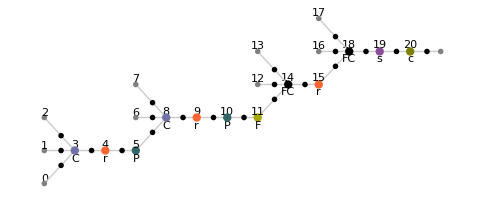

```mathematica
Information[uninitLeNet,"MXNetNodeGraphPlot"]
```

LeNet architecture starts at the input with the operation that converts the image to
a numeric array, followed by the first operation. This convolution returns a 20-feature
map with a rectified linear unit (ReLU) activation function immediately following
nodes 3 and 4. Then, the first max-pooling operation (subsampling layers) selects the
maximum value in the pooling node 5. Then, the second convolutional operation
returns a 50-feature map with a ReLU activation function immediately following nodes 8 and 9. The last convolution operation is followed by another max-pooling operation (node 10), followed by a flattening operation (node 11), which flattens the output of the pooling operation into a single vector. The last pooling operation gives an array of 50*4*4, and the flatten operation returns an 800-vector that is the input of the next operation. Next, you see the first fully connected layer (node 14); the first fully connected layer has a ReLU function (node 15), and the second fully connected layer has the softmax function (node 19). The last fully connected layer can be interpreted as a multilayer perceptron (MLP) that normalizes the output into a probability distribution to indicate the probability of each class. Finally, the tensor is converted to a class with the decoder. Nodes 4, 9, and 15 are the layers for non-linear operations (ReLU), and node 19 applies the softmax function for output classification. In summary, the architecture is as follows: Tensor (input), Convolution, ReLU, Pooling, Convolution, ReLU, Pooling, Flatten, Fully Connected (with ReLU), Fully Connected (with softmax), and Class output.

#### Preparing LeNet

Since LeNet is a neural network for image classification, an encoder and decoder must be used. The NetEncoder is inserted in the input NetPort, and the NetDecoder is on the output NetPort. Looking into the NetGraph might be useful in understanding the process inside the Wolfram Language. Clicking the input and output shows the relevant information.

```mathematica
NetGraph[uninitLeNet]
```

NetGraph[…]

You can extract the encoder and decoder to inspect their infrastructure. The encoder
receives an image of the dimensions of 28 x 28 of any color space and encodes the image into a color space set to grayscale, returning then an array of the size of 1 x 28 x 28. On the other hand, the decoder is a class decoder that receives a 10-size vector, which tells the probability for the class labels that are 0, 1, 2, 3, 4, 5, 6, 7, 8, and 9.

```mathematica
{enc=NetExtract[uninitLeNet,"Input"],dec=NetExtract[uninitLeNet,"Output"]}//Row
```

NetEncoder[…]NetDecoder[…]

First, let’s look at how the net model works with NetInitialize; for example, use an
image of 0 in the training set.

```mathematica
testNet=NetInitialize[uninitLeNet,RandomSeeding->8888];
testNet@trainData[[1,1]]
```

9

The net returns that the image belongs to class 9, which means that the image is
a number 9; clearly, this is wrong. Let’s try NetInitialize again but with the different
methods available. Writing all, as the second argument to NetInitialize, overwrites any
pre-existing learning parameters on the network.

```mathematica
{net1,net2,net3,net4}=
Table[NetInitialize[uninitLeNet,All,Method->i,RandomSeeding->8888],{i,{"Kaiming","Xavier","Orthogonal","Identity"}}];
{net1[trainData[[1,1]]],
net2[trainData[[1,1]]],
net3[trainData[[1,1]]],
net4[trainData[[1,1]]]}
```

{9,9,7,3}

Every net model fails to classify the image in the correct class. This result is because the neural network has not been trained, unlike NetInitialize, which only randomly initializes the learnable parameters without proper training. This is why, with NetInitialize, the model fails to classify the image given correctly. But first, let’s establish the network graph to better illustrate the model

```mathematica
leNet=NetInitialize[NetGraph[<|"LeNet NN"->uninitLeNet,"LeNet Loss"->CrossEntropyLossLayer@"Index"|>,{NetPort@"Input"->"LeNet NN","LeNet NN"->NetPort@{"LeNet Loss","Input"},NetPort@"Target"->NetPort@{"LeNet Loss","Target"}}],RandomSeeding->8888]
```

NetGraph[<2>, <4>]

Before you train the net, you must make the validation set suited for the
CrossEntropyLossLayer in the target input because the classes start at 0 and end at 9,
and the Index target begins at 1 and goes on. So, the target input needs to be between
1 and 10.

```mathematica
trainDts=Dataset@Join[AssociationThread["Input"->#]&/@Keys[trainData],AssociationThread["Target"->#]&/@Values[trainData]+1,2];
testDts=Dataset@Join[AssociationThread["Input"->#]&/@Keys[testData],AssociationThread["Target"->#]&/@Values[testData]+1,2];
```

The training set and validation set have the form of a dataset. Only four random
samples are shown.

```mathematica
BlockRandom[SeedRandom[999];{RandomSample[trainDts[[All]],4],RandomSample[testDts[[All]],4]}]
```

{,}

#### LeNet Training

Now that you have grasped the process of this neural net model, you can proceed to train the neural net model. With NetTrain, you gradually modify the learnable parameters of the neural network to reduce the loss. The next training code is set with the options seen in the previous section, but here, you add new options also available for training. The first one is TrainingProgressMeasurements. TrainingProgressMeasurements can specify measures such as accuracy and precision. These are measured during the training phase by round or batch. The ClassAveraging is used to specify to get the macro-average or the micro-average of the measurement specified <|“Measurement” -> “measurement” (Accuracy, RSquared, Recall, MeanSquared, etc.), “ClassAveraging”->“Macro”|>.

The second option is the TrainingStoppingCriterion, which is used to add an early
stopping to avoid overfitting during the training phase based on different criteria, such as stopping the training when the validation loss is not improving, measuring the absolute or relative change of a measurement (accuracy, precision, loss, etc.), or stopping the training when the loss or other criteria does not improve after a certain number of rounds <|Criterion->”measurement” (Accuracy, Loss, Recall, etc.), “Patience”-> # of rounds|>.

```mathematica
netResults=NetTrain[leNet,trainDts,All,ValidationSet->testDts,MaxTrainingRounds->15,BatchSize->2096,LearningRate->Automatic,Method->"ADAM",TargetDevice->"CPU",PerformanceGoal->"TrainingMemory",WorkingPrecision->"Real32",RandomSeeding->99999,TrainingProgressMeasurements->{<|"Measurement"->"Accuracy","ClassAveraging"->"Macro"|>,<|"Measurement"->"Precision","ClassAveraging"->"Macro"|>,<|"Measurement"->"F1Score","ClassAveraging"->"Macro"|>,<|"Measurement"->"Recall","ClassAveraging"->"Macro"|>,<|"Measurement"->"ROCCurvePlot","ClassAveraging"->"Macro"|>,<|"Measurement"->"ConfusionMatrixPlot","ClassAveraging"->"Macro"|>},TrainingStoppingCriterion-><|"Criterion"->"Loss","AbsoluteChange"->0.001|>]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:319  rounds:11  time:6.1min  examples/s:1832
data | ,,  training examples:60000  validation examples:10000  processed examples:668624  skipped examples:0
method | ,,  ADAMoptimizer  batch size2096CPU
round | ,,  loss:3.61×10^-2  acc.:98.87%  prec.:98.86%  F1:98.86%  recall:98.86%
validation | ,,  loss:3.92×10^-2  acc.:98.70%  prec.:98.71%  F1:98.69%  recall:98.68%
 | 
-Graphics-  training set	-Graphics-  validation set | ]

The final results of the training phase are depicted in the above.

Extracting the trained model and appending the net encoder and decoder is done
because the trained net does not come with an encoder and decoder at the input and
output ports.

```mathematica
NetExtract[netResults["TrainedNet"],"LeNet NN"];
trainedLeNet=NetReplacePart[%,{"Input"->enc,"Output"->dec}];
```

#### LeNet Model Assessment

The following grid shows the tracked measurements and plots of the training set. The measurements of the training set are in the RoundMeasurements property. To get the list of the values in each round, use RoundMeasurementsLists.

The performance of the training set is assessed with the round measurements, and the
test set is evaluated with the validation measurements. Also, the ROC curves and the
confusion matrix plot are shown in both cases.

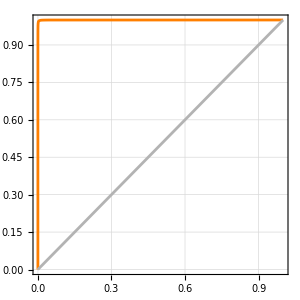
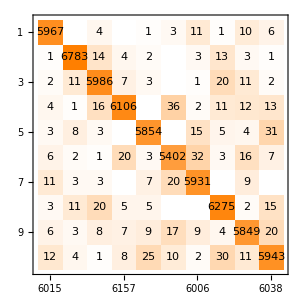
RoundMeasurements | ROCCurvePlot | ConfusionMatrixPlot
 | recall | -Graphics-
 | false positive rate | actual class | -Graphics-
 | predicted class

```mathematica
netResults["RoundMeasurements"][[1;;5]];
Normal[netResults["RoundMeasurements"][[6;;7]]];
Grid[{{Style["RoundMeasurements",#1,#2],Style[%[[1,1]],#1,#2],Style[%[[2,1]],#1,#2]},{Dataset[%%],%[[1,2]],%[[2,2]]}},Dividers->Center]&[Bold,FontFamily->"Alegraeya SC"]
```

To see how the model performed on the validation set, see ValidationMeasurements. To get the list of the values in each round, use ValidationMeasurementsLists.

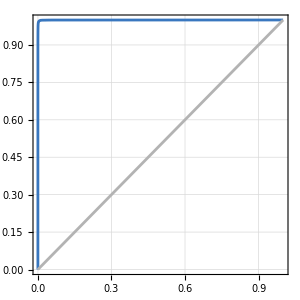
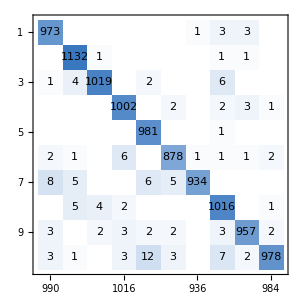
ValidationMeasurements | ROCCurvePlot | ConfusionMatrixPlot
 | recall | -Graphics-
 | false positive rate | actual class | -Graphics-
 | predicted class

```mathematica
netResults["ValidationMeasurements"][[1;;5]];
Normal[netResults["ValidationMeasurements"][[6;;7]]];
Grid[{{Style["ValidationMeasurements",#1,#2],Style[%[[1,1]],#1,#2],Style[%[[2,1]],#1,#2]},{Dataset[%%],%[[1,2]],%[[2,2]]}},Dividers->Center]&[Bold,FontFamily->"Alegraeya SC"]
```

#### Testing LeNet

Having finished the training and reviewed the round and validation measures, you are now ready to test the trained LeNet neural network with some difficult images to see how it performs.

```mathematica
expls=Keys[{testData[[2150]],testData[[3910]],testData[[6115]],testData[[6011]],testData[[7834]]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

The selected images belong to the numbers 2, 3, 6, 5, and 7.

```mathematica
trainedLeNet[expls,"TopProbabilities"]
```

{{2→0.997335},{3→0.999209},{6→0.547947,0→0.427594},{6→0.909045},{7→0.999774}}

```mathematica
TableForm[Transpose@{trainedLeNet[expls,{"TopDecisions",2}],trainedLeNet[expls,{"TopProbabilities",2}]},TableHeadings->{Map[ToString,{2,3,6,5,7},1],{"Top Decisions","Top Probabilities"}},TableAlignments->Center]
```

| Top Decisions | Top Probabilities
2 | 3
2 | 3→0.00248538
2→0.997335
3 | 9
3 | 9→0.000671447
3→0.999209
6 | 0
6 | 0→0.427594
6→0.547947
5 | 5
6 | 5→0.0856998
6→0.909045
7 | 3
7 | 3→0.00012312
7→0.999774

The trained net has misclassified the image of the number 5 because the top
decisions are either a 5 or a 6, being 6 with top probability, which is wrong. Also, you
can see the probabilities of the top decisions. Another form to evaluate the trained net
in the test set is using NetMeasurements to set the net model, test set, and the interested measure. In the example, the measure of interest is the ConfusionMatrixPlot.

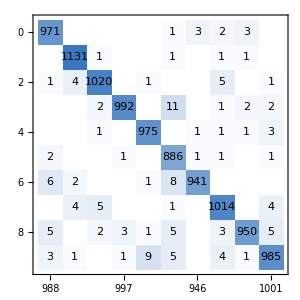
actual class | -Graphics-
 | predicted class

```mathematica
NetMeasurements[trainedLeNet,testData,"ConfusionMatrixPlot"]
```

### GPT and LLM Basics

This section explores the neural network GPT models available in the Wolfram
Language. You learn the basics of generative pre-trained transformers (GPT), the
architecture of some GPT models inside Mathematica, and new LLM (large language
model) Mathematica features.

#### A Brief Overview

GPT is a series of AI models that uses deep learning and transformer architecture
to generate human-like text by analyzing preceding text. LLM is a broader category
encompassing models trained to understand and generate human-readable text. GPT
models fall under the LLM category, representing just one kind of model within the
broader LLM framework.

#### LLM in the Wolfram Language

The Wolfram Language offers several new LLM-based functionalities, including the
following.
• Chat Notebooks: a new feature enabling efficient and accessible conversations with LLM (GPT-3, among others) like a traditional Mathematica notebook 
• Wolfram Prompt Repository: a collection of useful prompts made by a community for easy access to LLM scope applications
• LLM Function Integration: seamless incorporation of LLM functions
within Mathematica
• GPT-1 and GPT-2: available from the Wolfram Neural Net Repository

Note: For llm services in Mathematica, external apI access is needed. Ensure your apI key is valid; for example, for OpenAI, an active Chat Gpt account with billing details is required. Be aware that apI costs are separate from their subscription plans and vary based on the model used. Make sure to read OpenAI documentation for pricing and account details.

To connect to OpenAI GPT services, you first need to establish a connection. The
most direct path to connect is through the settings or preferences section. Select the AI
settings option from there, which shows various tabs related to chat notebooks, services, personas, and tools. The default tab has the general setting for the persona, LLM service, and temperature (model creativity), among other settings. To proceed, go to the Services tab and click Authentication, followed by Connect. This triggers a WolframConnector pop-up that requests the key access.

To get started, enter the key, save it by clicking the checkbox, and agree on the terms
of use. Once linked, a checkmark appears under Authentication. If a valid API is not linked, LLM services won’t work. To remove the key, click Disconnect and repeat the previous steps.

Note: For quick apI and llm support, visit https://support.wolfram.com/

#### Chat Notebooks

New types of notebooks have been developed apart from regular notebooks. These
notebooks are specialized for LLM tasks. These are Chat-Enabled and Chat-Driven
Notebooks. To create a new one, go to File ➤ New, then select Chat-Enabled or Chat-Driven Notebook. By default, chat-enabled use input chat cells with the code assistant persona (sets the LLM’s response style), while chat-driven cells use PlainChat (basic dialog, no Wolfram code execution)

Apart from the different cells, it show the various personas and GPT models for use. You can select the one that fits your needs. The base model version used in the following examples is with GPT-3.5 Turbo.

To create a new chat cell, press (‘) once. Press it twice for a side chat and three times
for chat system input. To enable it in a regular notebook, click the chat cell icon in the top right corner. Select “Enable AI chat features” to activate. Select the “Do automatic result analysis” option for LLM tips on output code. Try the example shown to see if everything is working.

If you open a AI-driven notebook, a chat icon is visible in the right cell bracket; this option lets you useLLM with Wolfram code like you use it in Mathematica. The chat history is sequential, and the conversation history output can also be accessed using the chat arrows. Side chat cells or blocks/delimiters separate chats. Distinct personas yield different responses; the CodeAssistant chat implies prompts in Wolfram code, whereas the Plain and RawChat yield output but do not imply that it’s related to Wolfram code (unless specified in the prompt), resulting in Python code being used instead. Hovering over the code part allows you to either insert it as a newly evaluated cell, insert it, or copy it.

Note: keep your prompts concise; always verify the chosen model to avoid unexpected fees since models have different costs based on token count.

Chat cells can rerun the prompt and regenerate the response. But remember that the
LLM prompts are not run by Mathematica kernel, so history is saved on the notebook. So, closing the notebook does not erase the conversation.

#### Wolfram Prompt Repository

The Wolfram Prompt Repository gives you access to a large, curated base of prompts, from LLM prompts, personas, and costume functions. Navigating is similar to other repositories. Select from the accessible sections to find your desired prompts or persona for costume-style conversations. Once a prompt is selected various options are available, like chat samples and how to use it inside Mathematica. The platform further supports uploading, downloading, and utilizing various LLM components

For instance, you can format output with different personas; select the persona from
the drop-down menu. To download a persona, go to the Personas tab in the AI setting and install via the prompt repository or enter the persona URL. Once installed, it should be available; this can also be done via Add & Manage Personas.

Apart from personas, a combination of prompt modifiers can be used. These act on the input or output of a prompt. So, to invoke an input persona, use the character
‘@persona.’ To call for a function input modifier, use ‘!prompt’; to call an output
modifier, use ‘#param ‘; input and output modifiers go at the beginning and end of the prompt. To insert parameters to function modifiers, use the vertical bar to separate, like ‘#prompt|param ‘

#### LLM Functionalities

Chat objects are used along with chat evaluate to manage LLM conversations within Mathematica. The chat object provides a convenient interface for interacting with the
LLM and managing conversations in a notebook environment. What happens is that
internally, LLM commands work as synthetic functions, which allows the LLM model to access the Wolfram tools.

```mathematica
ChatEvaluate[ChatObject[],"Break down this code in 3 simple points? For[i=1,i<=5,i++,Print[i]",LLMEvaluator-><|"Prompts"->{LLMPrompt["ELI5"]}|>]
```

ChatObject[…]

To retrieve the chat contents and tokens, use the words “Messages” and “Usage”.

```mathematica
%["Messages"]
%%["Usage"]
```

{<|Role→User,Content→{<|Type→Text,Data→Break down this code in 3 simple points? For[i=1,i<=5,i++,Print[i]|>},Timestamp→Wed 20 Nov 2024 14:18:40GMT+8|>,<|Content→{<|Type→Text,Data→1. **Start with 1**: We begin with a number called `i` and set it to 1.
2. **Count Up to 5**: We keep going up by 1 each time until `i` reaches 5.
3. **Say the Number**: Each time we go up, we say the number `i`.|>},ToolRequests→{},Timestamp→Wed 20 Nov 2024 14:18:45GMT+8,Role→Assistant|>}

114 tokens

Like the previous example, you can set a prompt with a specific configuration with
LLMConfiguration evaluated with LLMEvaluator, like the base model, temperature, stop tokens, and so forth. It can also be used to generate text (LLMSynthesize), retrieve text (LLMPrompt), or use a template function (LLMFunction), as the following code shows.

```mathematica
llmConfig=LLMConfiguration[<|"Prompts"->LLMPrompt["ELI5"],"Model"->"DeepSeek Chat","Temperature"->0.1,"MaxTokens"->5|>];
LLMSynthesize["Break down this code in 3 simple points? For[i=1,i<=5,i++,Print[i]",LLMEvaluator->llmConfig]
```

ServiceExecute::apierr: The service returned the following error message: Model Not Exist.

Failure[…]

Note: the default llm configuration is in $llmevaluator but can be overridden.

#### GTP-1 and GPT-2 Models

Besides external LLM services, open models like GPT-1 and GPT-2 are accessible in Mathematica. These models are predecessors to recent GPT models. GPT –1 is one of the initial models trained on a large book dataset, and GPT-2 is an improved version of GPT-1, trained on the WebText dataset. Let’s look at some information about GPT-1 and GPT-2; note that the output here is truncated, given the large text.

```mathematica
Row[{Short[NetModel["GPT Transformer Trained on BookCorpus Data",#]&/@{"Details","ShortName"}//Column,4],Short[NetModel["GPT2 Transformer Trained on WebText Data",#]&/@{"Details","ShortName"}//Column,4]}]
```

Released in 2018, this Generative Pre-Training Transf…attention, often referred to as a transformer decoder.
…Released in 2019, this model improves and scales up i…alization at the end of all of the transformer blocks.
…

You can try to retrieve other data, like in the LeNet example. Let’s look at model
variants and task types examples.

```mathematica
NetModel["GPT Transformer Trained on BookCorpus Data",#]&/@{"ParametersAllowedValues","Variants"}
NetModel["GPT2 Transformer Trained on WebText Data",#]&/@{"ParametersAllowedValues","Variants"}
```

{<|Task→{FeatureExtraction,LanguageModeling}|>,{{GPT Transformer Trained on BookCorpus Data,Task→FeatureExtraction},{GPT Transformer Trained on BookCorpus Data,Task→LanguageModeling}}}

{<|Task→{FeatureExtraction,LanguageModeling},Size→{117M,345M,774M}|>,{{GPT2 Transformer Trained on WebText Data,Task→FeatureExtraction,Size→117M},{GPT2 Transformer Trained on WebText Data,Task→FeatureExtraction,Size→345M},{GPT2 Transformer Trained on WebText Data,Task→FeatureExtraction,Size→774M},{GPT2 Transformer Trained on WebText Data,Task→LanguageModeling,Size→117M},{GPT2 Transformer Trained on WebText Data,Task→LanguageModeling,Size→345M},{GPT2 Transformer Trained on WebText Data,Task→LanguageModeling,Size→774M}}}

As seen in the output, variants have different task types and a specific number of
parameter sizes, like 117M, 354M, and 774M million parameters. You can pick a model by specifying the parameters, for instance, picking the language-trained model and trying to generate text based on the prediction of the next token.

```mathematica
gpt1=NetModel[{"GPT Transformer Trained on BookCorpus Data","Task"->"LanguageModeling"}]
gpt2=NetModel[{"GPT2 Transformer Trained on WebText Data","Task"->"LanguageModeling"}]
```

NetChain[<5>]

NetChain[<5>]

For the token function, the input parameters are the initial text, token count (default
10), and temperature (default 1). In simple terms, this function samples predictions. It
attaches each new token to the original string for the fixed token count and returns the
initial text plus the generated tokens text.

```mathematica
generateText[LLmodel_][initialText_,tokenCount_:10,temperature_:1]:=Fold[StringJoin[#1,LLmodel[#1,{"RandomSample","Temperature"->temperature}]]&,initialText,Range[tokenCount]]
```

Where a token refers to a unit of text that the model reads. It can be as short as one
character or as long as one word, like “a” or “app.” The model looks at these tokens
individually to understand and generate text based on them. So, for GPT-2, BPE
tokenization is a method used to break down words into smaller parts.

```mathematica
generateText[gpt1]["Alan Turing was a British mathematician and logician who is considered a pioneer in the field of computer science.",20,0.5]
```

Alan Turing was a British mathematician and logician who is considered a pioneer in the field of computer science.he is a brilliant mathematician who is also a brilliant scientist . his work is a work of fiction .

```mathematica
generateText[gpt2]["Alan Turing was a British mathematician and logician who is considered a pioneer in the field of computer science.",20,1]
```

Alan Turing was a British mathematician and logician who is considered a pioneer in the field of computer science. Turing first programmed computers to write colour codes , every bit as complex as pieces of shorthand. Then,

As seen comparing both responses, there is still room for improvement. GPT-1
output seems incoherent with unrelated elements. In contrast, GPT-2 shows more
context talking about Turing’s career but still lacks clear, complete sentences.

### Final Remarks

In summary, the following road map for the general schematics, construction, testing,
and implementation of a machine learning or a neural network model within the
Wolfram Language scheme are in

The diagram shows a route that can be followed directly; despite this, there may be
intermediate points between each process within the route since the route may vary
depending on the type of task or problem being solved. However, the route focuses on
exposing the important and general points to construct a model using the Wolfram
Language. Within the data preparation phase are previous processes, such as data
integration, the type of data collected (structured or unstructured), transformations in
the data, cleaning in data modules, and so on. So before moving on to the next phase,
there must be a pre-processing of the data, to have data ready to be fed to the model.

Model preparation covers aspects such as the choice of the algorithm or the methods
to use, depending on the type of learning; establishing or detecting the structure of the
model; and defining the characteristics, input parameters, and type of data that is used, whether it be text, sound, numerical data, and tools to be used. All this is linked to a process called feature engineering, whose primary goal is to extract valuable attributes from data. This is needed to move on to the next point, the training phase.

The evaluation phase and model assessment consists of defining the evaluation
metrics, which vary according to the task or problem being solved, and preparing the
validation used later. The model’s output is converted back to a clear, interpretable
format at the decoding phase, readying for practical use. At this point, it is necessary to emphasize that the preparation of the model, training, evaluation, and assessment can be an iterative process, including tuning of hyperparameters, adjustments on algorithm techniques, and model configurations such as internal model features. The purpose is to establish the best possible model capable of delivering adequate results and finally reaching the model deployment phase, which defines the model chosen and tested on new data.